```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ReadAMBiTOutput`
```

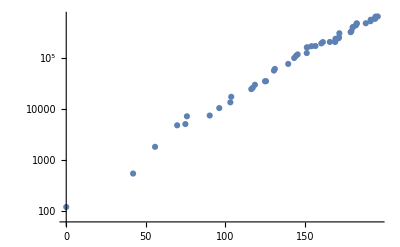

1.51673

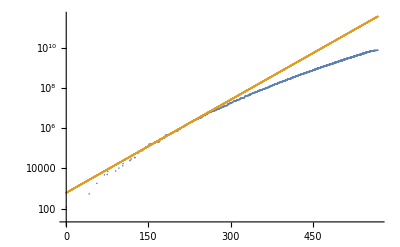

A: 610.388

ϵ: 28.149 ± 1.51673

```mathematica
ion="07";
filename="C:\Users\mattb\Documents\Mathematica\Try_3\LevelDensity\Levels\Sn"<>ion<>"+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
Energy=(Energy-Min[Energy])*27.211;
L=Length[Energy];
n=Accumulate[Num];
ListLogPlot[{Energy,n}ᵀ[[1;;50]]]

fit=NonlinearModelFit[{Energy,n}ᵀ[[1;;50]],{A Exp[x/e0]},{{A,1},{e0,20}},x,ConfidenceLevel->.95];
fitVal=fit["BestFitParameters"];
ConfInt=fit["ParameterConfidenceIntervals"];
σ95=(ConfInt[[2]][[2]]-ConfInt[[2]][[1]])/2
A1=A/.fitVal;
e1=e0/.fitVal;
X=Range[0,Max[Energy],0.1];
Y=A Exp[X/e0]/.fitVal;
ListLogPlot[{{Energy,n}ᵀ,{X,Y}ᵀ}]
Print["A: ",A1]
Print["ϵ: ",e1," ± ",σ95]
```

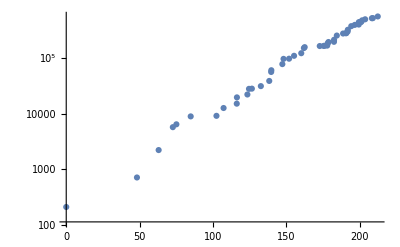

1.79437

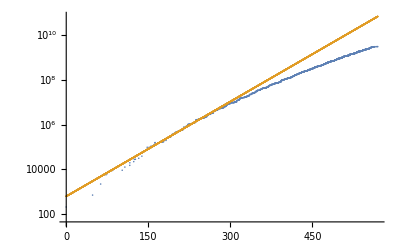

A: 628.196

ϵ: 30.76 ± 1.79437

```mathematica
ion="08";
filename="C:\Users\mattb\Documents\Mathematica\Try_3\LevelDensity\Levels\Sn"<>ion<>"+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
Energy=(Energy-Min[Energy])*27.211;
L=Length[Energy];
n=Accumulate[Num];
ListLogPlot[{Energy,n}ᵀ[[1;;50]]]

fit=NonlinearModelFit[{Energy,n}ᵀ[[1;;50]],{A Exp[x/e0]},{{A,1},{e0,20}},x,ConfidenceLevel->.95];
fitVal=fit["BestFitParameters"];
ConfInt=fit["ParameterConfidenceIntervals"];
σ95=(ConfInt[[2]][[2]]-ConfInt[[2]][[1]])/2
A1=A/.fitVal;
e1=e0/.fitVal;
X=Range[0,Max[Energy],0.1];
Y=A Exp[X/e0]/.fitVal;
ListLogPlot[{{Energy,n}ᵀ,{X,Y}ᵀ}]
Print["A: ",A1]
Print["ϵ: ",e1," ± ",σ95]
```

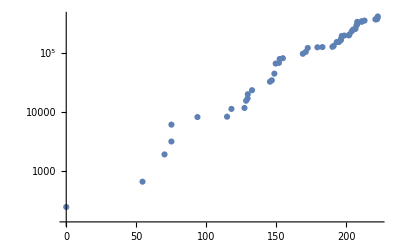

2.88957

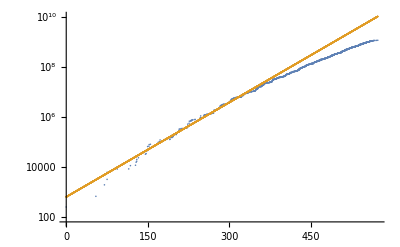

A: 636.665

ϵ: 34.5239 ± 2.88957

```mathematica
ion="09";
filename="C:\Users\mattb\Documents\Mathematica\Try_3\LevelDensity\Levels\Sn"<>ion<>"+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
Energy=(Energy-Min[Energy])*27.211;
L=Length[Energy];
n=Accumulate[Num];
ListLogPlot[{Energy,n}ᵀ[[1;;50]]]

fit=NonlinearModelFit[{Energy,n}ᵀ[[1;;50]],{A Exp[x/e0]},{{A,1},{e0,20}},x,ConfidenceLevel->.95];
fitVal=fit["BestFitParameters"];
ConfInt=fit["ParameterConfidenceIntervals"];
σ95=(ConfInt[[2]][[2]]-ConfInt[[2]][[1]])/2
A1=A/.fitVal;
e1=e0/.fitVal;
X=Range[0,Max[Energy],0.1];
Y=A Exp[X/e0]/.fitVal;
ListLogPlot[{{Energy,n}ᵀ,{X,Y}ᵀ}]
Print["A: ",A1]
Print["ϵ: ",e1," ± ",σ95]
```

1042

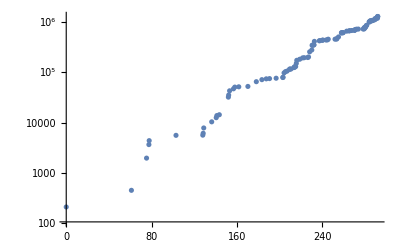

2.0089

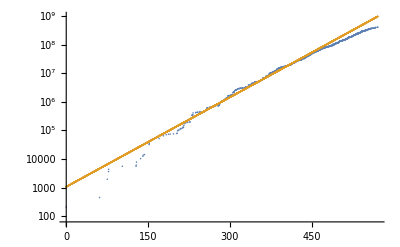

A: 1069.

ϵ: 41.6172 ± 2.0089

```mathematica
ion="10";
filename="C:\Users\mattb\Documents\Mathematica\Try_3\LevelDensity\Levels\Sn"<>ion<>"+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
Energy=(Energy-Min[Energy])*27.211;
L=Length[Energy]
n=Accumulate[Num];
ListLogPlot[{Energy,n}ᵀ[[1;;100]]]

fit=NonlinearModelFit[{Energy,n}ᵀ[[1;;100]],{A Exp[x/e0]},{{A,1},{e0,20}},x,ConfidenceLevel->.95];
fitVal=fit["BestFitParameters"];
ConfInt=fit["ParameterConfidenceIntervals"];
σ95=(ConfInt[[2]][[2]]-ConfInt[[2]][[1]])/2
A1=A/.fitVal;
e1=e0/.fitVal;
X=Range[0,Max[Energy],0.1];
Y=A Exp[X/e0]/.fitVal;
ListLogPlot[{{Energy,n}ᵀ,{X,Y}ᵀ}]
Print["A: ",A1]
Print["ϵ: ",e1," ± ",σ95]
```

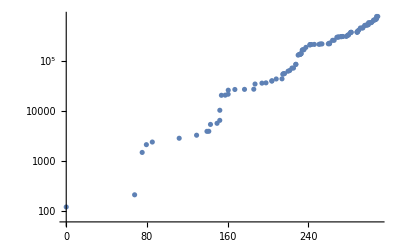

1.88143

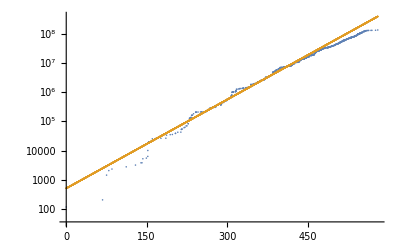

A: 519.741

ϵ: 42.9832 ± 1.88143

```mathematica
ion="11";
filename="C:\Users\mattb\Documents\Mathematica\Try_3\LevelDensity\Levels\Sn"<>ion<>"+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
Energy=(Energy-Min[Energy])*27.211;
L=Length[Energy];
n=Accumulate[Num];
ListLogPlot[{Energy,n}ᵀ[[1;;100]]]

fit=NonlinearModelFit[{Energy,n}ᵀ[[1;;100]],{A Exp[x/e0]},{{A,1},{e0,20}},x,ConfidenceLevel->.95];
fitVal=fit["BestFitParameters"];
ConfInt=fit["ParameterConfidenceIntervals"];
σ95=(ConfInt[[2]][[2]]-ConfInt[[2]][[1]])/2
A1=A/.fitVal;
e1=e0/.fitVal;
X=Range[0,Max[Energy],0.1];
Y=A Exp[X/e0]/.fitVal;
ListLogPlot[{{Energy,n}ᵀ,{X,Y}ᵀ}]
Print["A: ",A1]
Print["ϵ: ",e1," ± ",σ95]
```

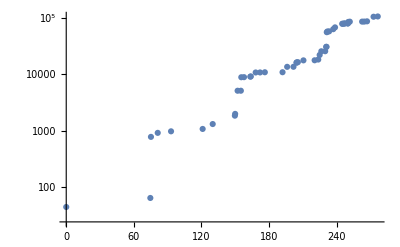

6.20886

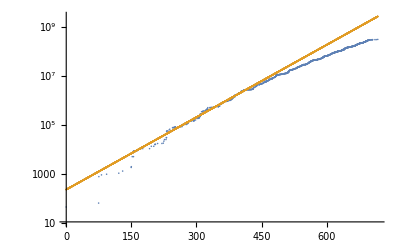

A: 231.884

ϵ: 44.0085 ± 6.20886

```mathematica
ion="12";
filename="C:\Users\mattb\Documents\Mathematica\Try_3\LevelDensity\Levels\Sn"<>ion<>"+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
Energy=(Energy-Min[Energy])*27.211;
L=Length[Energy];
n=Accumulate[Num];
ListLogPlot[{Energy,n}ᵀ[[1;;50]]]

fit=NonlinearModelFit[{Energy,n}ᵀ[[1;;50]],{A Exp[x/e0]},{{A,1},{e0,20}},x,ConfidenceLevel->.95];
fitVal=fit["BestFitParameters"];
ConfInt=fit["ParameterConfidenceIntervals"];
σ95=(ConfInt[[2]][[2]]-ConfInt[[2]][[1]])/2
A1=A/.fitVal;
e1=e0/.fitVal;
X=Range[0,Max[Energy],0.1];
Y=A Exp[X/e0]/.fitVal;
ListLogPlot[{{Energy,n}ᵀ,{X,Y}ᵀ}]
Print["A: ",A1]
Print["ϵ: ",e1," ± ",σ95]
```

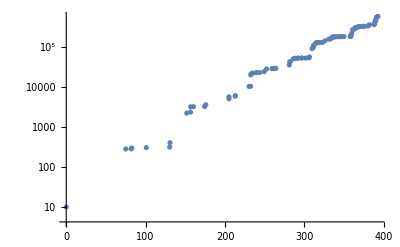

2.80273

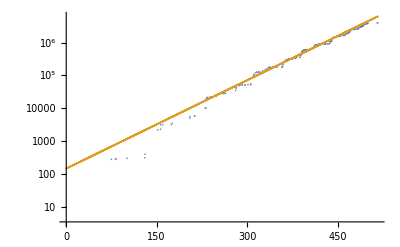

A: 147.695

ϵ: 48.5075 ± 2.80273

```mathematica
ion="13";
filename="C:\Users\mattb\Documents\Mathematica\Try_3\LevelDensity\Levels\Sn"<>ion<>"+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
Energy=(Energy-Min[Energy])*27.211;
L=Length[Energy];
n=Accumulate[Num];
ListLogPlot[{Energy,n}ᵀ[[1;;100]]]

fit=NonlinearModelFit[{Energy,n}ᵀ[[1;;100]],{A Exp[x/e0]},{{A,1},{e0,20}},x,ConfidenceLevel->.95];
fitVal=fit["BestFitParameters"];
ConfInt=fit["ParameterConfidenceIntervals"];
σ95=(ConfInt[[2]][[2]]-ConfInt[[2]][[1]])/2
A1=A/.fitVal;
e1=e0/.fitVal;
X=Range[0,Max[Energy],0.1];
Y=A Exp[X/e0]/.fitVal;
ListLogPlot[{{Energy,n}ᵀ,{X,Y}ᵀ}]
Print["A: ",A1]
Print["ϵ: ",e1," ± ",σ95]
```

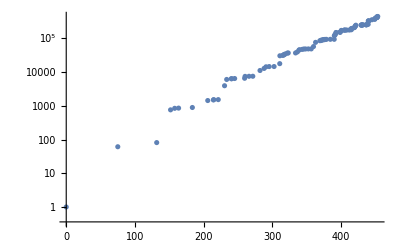

1.86539

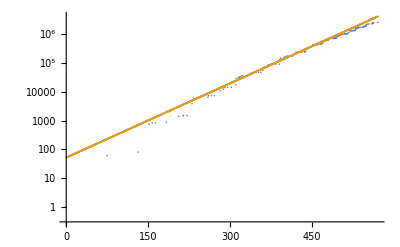

A: 52.3754

ϵ: 50.4918 ± 1.86539

```mathematica
ion="14";
filename="C:\Users\mattb\Documents\Mathematica\Try_3\LevelDensity\Levels\Sn"<>ion<>"+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
Energy=(Energy-Min[Energy])*27.211;
L=Length[Energy];
n=Accumulate[Num];
ListLogPlot[{Energy,n}ᵀ[[1;;100]]]

fit=NonlinearModelFit[{Energy,n}ᵀ[[1;;100]],{A Exp[x/e0]},{{A,1},{e0,20}},x,ConfidenceLevel->.95];
fitVal=fit["BestFitParameters"];
ConfInt=fit["ParameterConfidenceIntervals"];
σ95=(ConfInt[[2]][[2]]-ConfInt[[2]][[1]])/2
A1=A/.fitVal;
e1=e0/.fitVal;
X=Range[0,Max[Energy],0.1];
Y=A Exp[X/e0]/.fitVal;
ListLogPlot[{{Energy,n}ᵀ,{X,Y}ᵀ}]
Print["A: ",A1]
Print["ϵ: ",e1," ± ",σ95]
```